-Graphics-

# Wolfram Language

## Quantity and Date Frameworks

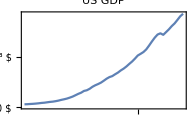

-Graphics-

## Objectives

This talk will go over the following frameworks:

Quantity

DateObject

## Quantity

A Quantity object is a data structure with a magnitude and a unit:

```mathematica
Quantity[3,"Meters"]
```

3 m

### Magnitude

The magnitude can be any Mathematica expression, although using numbers and variables would be natural:

```mathematica
Quantity[x^2+y,"Meters"]
```

(x^2+y) m

The magnitude can be a list, in which case Quantity threads over the list:

```mathematica
Quantity[{1,2,3},"Grams"]
%//InputForm
```

{1 g,2 g,3 g}

{Quantity[1, "Grams"], Quantity[2, "Grams"], Quantity[3, "Grams"]}

If no magnitude is given, then it is assumed to be 1:

```mathematica
Quantity["Seconds"]
%//InputForm
```

1 s

Quantity[1, "Seconds"]

Finally, it is possible to use a magnitude of None, in which case no magnitude is displayed:

```mathematica
Quantity[None, "Hours"]
```

h

### Units

Units supported by Mathematica includes all those specified by NIST Special Publication 811http://www.nist.gov/pml/pubs/sp811/index.cfm. However, this is not very useful without some sort of discovery interface.

There is one local and 3 internet connected methods that one can use for unit discovery:

Autocomplete:

```mathematica
Quantity[1, ]
```

Linguistic discovery with LinguisticAssistant (Ctrl - =), using an internet connection to WolframAlpha:

```mathematica
LinguisticAssistant
```

Another similar method is to use the WolframAlpha function:

```mathematica
WolframAlpha["3 ft/s","MathematicaResult"]
%//InputForm
```

3 ft/s

Quantity[3, "Feet"/"Seconds"]

Finally, Quantity itself use linguistic discovery for simple string units:

```mathematica
Quantity[3, "m"]
%//InputForm
```

3 m

Quantity[3, "Meters"]

This mechanism doesn’t work for compound units:

```mathematica
Quantity[3, "m"/"Seconds"]
```

Quantity::unkunit: Unable to interpret unit specification m/Seconds.

Quantity[3,m/Seconds]

There is a DateUnit wrapper, for use in functions like InflationAdjust:

```mathematica
q = Quantity[100, DatedUnit["Yen",1969]]
```

100 ¥(Japanese yen1969)

Account for inflation between 1969 and today:

```mathematica
InflationAdjust[q, 2018]
```

340.307 ¥(Japanese yen2018)

It is also possible to use the wrapper IndependentUnit to create your own units:

```mathematica
Quantity[25,IndependentUnit["box"]/"Seconds"]
```

25 box/s

The argument to IndependentUnit must be a string in order to create a valid Quantity object.

### MixedMagnitude/MixedUnit

It is possible to create a mixed Quantity object by using MixedMagnitude and MixedUnit:

```mathematica
Quantity[MixedMagnitude[{5, 11}],MixedUnit[{"Feet","Inches"}]]
```

5 11

The current average time for the length of an MLB baseball game:

```mathematica
Quantity[MixedMagnitude[{3,5}],MixedUnit[{"Hours","Minutes"}]]
```

3 5

Note that like compound units, the Quantity linguistic discovery mechanism doesn’t work for MixedUnit objects.

### Attibutes

Interestingly, Quantity has the HoldRest attribute:

```mathematica
Attributes[Quantity]
```

{HoldRest,NHoldRest,Protected,ReadProtected}

This allows the use of units which would change upon evaluation:

```mathematica
Quantity[10,"Meters"/"Meters"]
```

10 m/m

### Formatting

Quantity objects have different formats depending on the FormatType that is being used. For example:

```mathematica
Quantity[1, "Meters"/"Seconds"]//InputForm
```

Quantity[1, "Meters"/"Seconds"]

```mathematica
Quantity[1, "Meters"/"Seconds"]//OutputForm
```

1 meter per second

```mathematica
Quantity[1, "Meters"/"Seconds"]//StandardForm
```

1 m/s

```mathematica
Quantity[1, "Meters"/"Seconds"]//TraditionalForm
```

1 m/s

Notice how when using OutputForm, the unit name changes depending on whether the magnitude is unity:

```mathematica
Quantity[1,"Feet"]//OutputForm
Quantity[2,"Feet"]//OutputForm
```

1 foot

2 feet

## Quantity Related Functions

### QuantityMagnitude

QuantityMagnitude can be used to extract the magnitude of a Quantity object:

```mathematica
QuantityMagnitude[Quantity[3, "barns"]]
```

3

When given a list of Quantity objects, QuantityMagnitude threads over the list:

```mathematica
QuantityMagnitude[{Quantity[3,"m"],Quantity[2,"ft"]}]
```

{3,2}

QuantityMagnitude also works for other objects, like a TimeSeries object. Here is a time series:

```mathematica
ts = Entity["Country","UnitedStates"]["GDP",{"Date"->All}]
```

TimeSeries[…]

The output of QuantityMagnitude:

```mathematica
values = QuantityMagnitude[ts]
```

TimeSeries[…]

Compare the output of the two time series:

```mathematica
ts[DateObject[{1960,1,1}]]
values[DateObject[{1960,1,1}]]
```

5.433×10^11 $

5.433×10^11

A mixed Quantity object:

```mathematica
QuantityMagnitude[Quantity[MixedMagnitude[{5,11}],MixedUnit[{"Feet","Inches"}]]]
```

MixedMagnitude[{5,11}]

### QuantityUnit

QuantityUnits extracts the unit from a Quantity object:

```mathematica
QuantityUnit[Quantity[3,"lbs"]]
```

Pounds

Recall that Quantity has the attribute HoldRest. If the unit would change upon evaluation, then QuantityUnit wraps a HoldForm around the output:

```mathematica
QuantityUnit[Quantity[10,"Meters"/"Meters"]]
%//InputForm
```

Meters/Meters

HoldForm["Meters"/"Meters"]

QuantityUnit returns “DimensionlessUnit” for NumericQ arguments:

```mathematica
QuantityUnit[Sqrt[2]]
```

DimensionlessUnit

Other uses of QuantityUnit are similar to QuantityMagnitude.

### QuantityQ

The predicate QuantityQ can be used to check the validity of a Quantity object:

```mathematica
QuantityQ[Quantity[23,"b"]]
QuantityQ[Quantity[13,x]]
```

True

False

```mathematica
QuantityQ[Quantity[10,IndependentUnit["blocks"]]]
QuantityQ[Quantity[10,IndependentUnit[x]]]
```

True

False

### KnownUnitQ

KnownUnitQ can be used to check the validity of a unit expression:

```mathematica
KnownUnitQ["Meters"/"Seconds"]
```

True

There is no linguistic discovery process for KnownUnitQ:

```mathematica
KnownUnitQ["m"]
```

False

KnownUnitQ has the attribute HoldAll, so that it can check units that would change upon evaluation:

```mathematica
KnownUnitQ["Meters"/"Meters"]
```

True

The evaluated version is not a valid unit:

```mathematica
KnownUnitQ[1]
```

False

### UnitDimensions

UnitDimensions returns a list of base dimensions associated with a unit:

```mathematica
UnitDimensions["Newton"]
```

{{LengthUnit,1},{MassUnit,1},{TimeUnit,-2}}

It is also possible to give a Quantity object as an argument:

```mathematica
UnitDimensions[Quantity[1, "USDollars"/"Years"]]
```

{{MoneyUnit,1},{TimeUnit,-1}}

Unlike KnownUnitQ, UnitDimensions will attempt to parse an unknown unit string:

```mathematica
UnitDimensions["m"]
```

{{LengthUnit,1}}

On the other hand, unlike Quantity, UnitDimensions does not have command completion:

```mathematica
UnitDimensions[]
```

The documentation for UnitDimensions gives the following list of possible dimensions:

Physical dimensions are: "AmountUnit", "ElectricCurrentUnit", "LengthUnit", "LuminousIntensityUnit", "MassUnit", "TemperatureUnit", and "TimeUnit".

Additional unit dimensions include: "AngleUnit", "InformationUnit", "MoneyUnit", "PersonUnit", "SolidAngleUnit", and "TemperatureDifferenceUnit".

It is possible to use the above dimensions to determine the possible canonical units.

```mathematica
dimensions={"AmountUnit","ElectricCurrentUnit","LengthUnit","LuminousIntensityUnit","MassUnit","TemperatureUnit","TimeUnit","AngleUnit","InformationUnit","MoneyUnit","PersonUnit","SolidAngleUnit","TemperatureDifferenceUnit"};
```

Removing the string Unit from each dimensions creates a list of physical quantities:

```mathematica
pq = StringTrim[dimensions,"Unit"]
```

{Amount,ElectricCurrent,Length,LuminousIntensity,Mass,Temperature,Time,Angle,Information,Money,Person,SolidAngle,TemperatureDifference}

Then, we can use QuantityVariableCanonicalUnit to determine the canonical unit for each physical quantity:

```mathematica
Table[
	QuantityVariableCanonicalUnit[QuantityVariable[p]],
	{p, pq}
]
```

{Moles,Amperes,Meters,Candelas,Kilograms,Kelvins,Seconds,Radians,Bits,USDollars,People,Steradians,KelvinsDifference}

### UnitConvert

UnitConvert with a single argument converts to SI base units. For example:

```mathematica
UnitConvert["Newtons"]
```

1 kg m/s^2

Like UnitDimension, UnitConvert also attempts to parse simple strings:

```mathematica
UnitConvert["earths gravity"]
```

196133/20000 m/s^2

The argument can also be a Quantity object:

```mathematica
UnitConvert[Quantity[1000, "amu"]]
```

1.660539×10^-24 kg

Associations will have their values converted:

```mathematica
UnitConvert[<|"Universe"->"mass of universe","Sun"->"mass of sun","Earth"->"mass of earth","Electon"->"electron mass"|>]
```

<|Universe→mass of universe,Sun→mass of sun,Earth→mass of earth,Electon→electron mass|>

The volume of different bottles of wines:

```mathematica
sizes={"Methuselahs","Salmanazars","Nebuchadnezzars","Melchiors"};
N@UnitConvert[AssociationThread[sizes->sizes],"Gallons"]
```

<|Methuselahs→1.58503 gal,Salmanazars→2.37755 gal,Nebuchadnezzars→3.96258 gal,Melchiors→4.7551 gal|>

With two arguments, UnitConvert will attempt to convert to the target unit. For instance:

```mathematica
UnitConvert[Quantity[1.8,"m"], MixedUnit[{"Feet","Inches"}]]
```

5 10.8661

It is also possible to convert to one of the following unit system, “SI”, “Imperial”, or “Metric”:

```mathematica
UnitConvert[Quantity[0, "DegreesCelsius"],"Imperial"]
```

32 °F

### UnitSimplify

UnitSimplify uses heuristic methods to simplify a unit into a simpler equivalent unit:

```mathematica
UnitSimplify[Quantity[10, "Newtons" "Meters"]]
```

10 J

## Functions Supporting Quantity

Many numeric functions in Mathematica have been overloaded to properly handle Quantity objects.

### Arithmetic

Compatible Quantity objects can be added:

```mathematica
Quantity[1,"Meters"]+Quantity[1,"Yards"]
```

2393/1143 yd

Quantity objects with incompatible dimensions generate an error message:

```mathematica
Quantity[1,"Meters"]+Quantity[1,"s"]
```

Quantity::compat: Seconds and Meters are incompatible units

1 m+1 s

CompatibleUnitQ can be used to check for incompatibility:

```mathematica
CompatibleUnitQ[Quantity[1,"Meters"], Quantity[1,"s"]]
```

False

With multiplication and division there is no concern about compatible dimensions:

```mathematica
Quantity[1,"Meters"]/Quantity[10,"s"]
```

1/10 m/s

Many other mathematical functions also support Quantity. One more example:

```mathematica
Round[Quantity[10,"Meters"],Quantity[ "Inches"]]
```

394 in

### Relational Operators

Relational operators like GreaterThan support Quantity objects:

```mathematica
Quantity[1,"Meters"]>Quantity[1,"Yards"]
```

True

Equal:

```mathematica
Quantity[1,"Days"]==Quantity[24,"Hours"]
```

True

Sort sorts Quantity objects based on their numerical values, just like Sort does for numbers:

```mathematica
sort=Sort[{Quantity[1,"Pints"],Quantity[1,"Teaspoons"],Quantity[1,"DropsUK"],Quantity[1,"Centiliters"]}]
```

{1 UK drop,1 tsp,1 cL,1 pt}

Check:

```mathematica
N@UnitConvert[sort, "pt"]
```

{0.000125099 pt,0.0104167 pt,0.0211338 pt,1. pt}

Note that just like for numerical quantities, Sort uses a canonical sort for exact expressions:

```mathematica
Sort[{1, Pi, 4}]
Sort[{Quantity[1,"m"],Quantity[Pi,"m"],Quantity[4,"m"]}]
```

{1,4,π}

{1 m,4 m,π m}

Use NumericalSort if you want to guarantee that numbers are sorted by their values:

```mathematica
NumericalSort[{Quantity[1,"Meters"],Quantity[Pi,"Meters"],Quantity[4,"Meters"]}]
```

{1 m,π m,4 m}

### List constructors

Iterators in general support Quantity objects:

```mathematica
Range[Quantity[0,"m"], Quantity[.001,"Miles"],Quantity[1,"ft"]]
```

{0 m,381/1250 m,381/625 m,1143/1250 m,762/625 m,381/250 m}

### Plotting

Plotting functions also support Quantity objects:

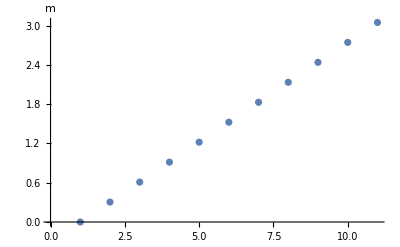

```mathematica
ListPlot[Range[Quantity[0,"ft"], Quantity[10,"ft"]],TargetUnits->"Meters", AxesLabel->Automatic]
```

### FormulaData

FormulaData makes extensive use of Quantity objects. A couple examples:

Escape velocity:

```mathematica
FormulaData["EscapeVelocity",{"m"->Quantity[1, "EarthMass"],"r"->Quantity[1, "EarthMeanRadius"]}]
```

v Speed==11185.9717987297 m/s

Plancks radiation law:

```mathematica
equation = Simplify[
	FormulaData[
		{"PlanckRadiationLaw", "Wavelength"},
		{"T"->Quantity[5000,"K"],"λ"->Quantity[wl,"μm"]}
	],
	wl≠0
]
```

L[λ] SpectralRadianceWRTWavelength==(1.19104×10^14 Pa/s)/((-1.+ⅇ^(2.87755/wl)) wl^5)

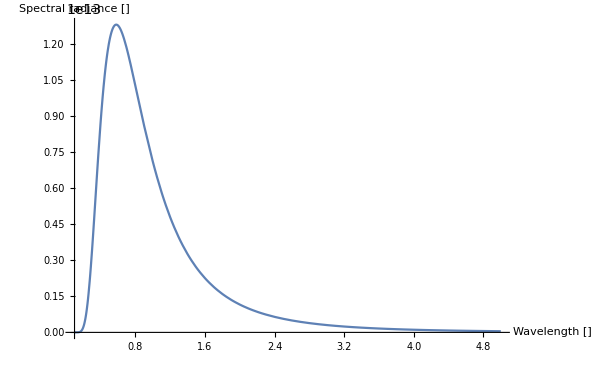

```mathematica
Plot[
	equation⟦2⟧,
	{wl, 0.1, 5},
	AxesLabel -> {
		StringForm[
			"Wavelength [`1`]",
			TraditionalForm@Quantity[None,"μm"]
		],
		StringForm[
			"Spectral radiance [`1`]",
			TraditionalForm[Quantity[None,"Watts""Steradians"^-1"Meters"^-3]]
		]
	},
	ImageSize->600
]
```

## QuantityArray

When working with a list of Quantity objects, a couple issues arise. First, the memory footprint of Quantity objects can be rather large. Second, the computational performance can be poor. To rectify these problems, one can use QuantityArray objects.

### Construction

To construct a QuantityArray, just use a QuantityArray head instead of Quantity:

```mathematica
QuantityArray[{1,2,3}, "m"]
```

QuantityArray[…]

Note that the first argument must be a rectangular array:It is also possible to mix units:

```mathematica
QuantityArray[{1, {2,3}}, "m"]
```

QuantityArray::rect: Nonrectangular array encountered.

QuantityArray[{1,{2,3}},m]

QuantityArray (as a constructor) will also convert arrays of Quantity objects into a QuantityArray:

```mathematica
QuantityArray[{Quantity[1,"m"], Quantity[2,"ft"], Quantity[3,"s"]}]
```

QuantityArray[…]

Use Normal to convert from a QuantityArray to a list of Quantity objects:

```mathematica
nqa = Normal[QuantityArray[{1,2,3}, {"m","m","yd"}]]
nqa//InputForm
```

{1 m,2 m,3 yd}

{Quantity[1, "Meters"], Quantity[2, "Meters"], 
 Quantity[3, "Yards"]}

And converting back:

```mathematica
QuantityArray[nqa]
```

QuantityArray[…]

### Benefits

#### Memory

Here' s an example of a QuantityArray created by GeoElevationData:

```mathematica
qa=GeoElevationData[GeoDisk[Entity["City",{"LaPaz","LaPaz","Bolivia"}],Quantity[3, "Miles"]]]
```

QuantityArray[…]

The corresponding Quantity version:

```mathematica
nqa = Normal @ qa; //AbsoluteTiming
```

{2.32137,Null}

As you can see, just converting from a QuantityArray to a normal list of Quantity objects can be time consuming. Now, compare the memory use of the QuantityArray object, and the corresponding Quantity version:

```mathematica
b1 = ByteCount[qa]
b2 = ByteCount[nqa]
N[b1/b2]
```

535040

7536968

0.0709888

Quite a bit smaller.

### Speed

We saw earlier that just converting from a QuantityArray object to a list of Quantity objects is time consuming. Working with lists of Quantity objects is also slower than working with a QuantityArray object:

```mathematica
QuantityMagnitude[qa]; //AbsoluteTiming
QuantityMagnitude[nqa];//AbsoluteTiming
```

{0.000097,Null}

{0.743024,Null}

## DateObject

The Date framework contains many functions, but the main expression is DateObject.

### Construction

DateObject with no arguments returns the current time:

```mathematica
DateObject[]
```

Thu 28 Jun 2018 01:18:45GMT-4.

This is equivalent to using Now:

```mathematica
Now
```

Thu 28 Jun 2018 01:19:06GMT-4.

DateObject can accept a list of up to 6 elements, corresponding to the year, month, day, hour and second. It will return a DateObject with a granularity that depends on the specificity of the input:

```mathematica
DateObject[{2018}]
DateObject[{2018, 7}]
DateObject[{2018, 7, 1, 10}]
```

Year: 2018

Month: Jul 2018

Hour: Sun 1 Jul 2018 10 amGMT-4.

DateObject can also accept a string input:

```mathematica
DateObject["June 28, 2018"]
```

Day: Thu 28 Jun 2018

Just like with lists, the granularity of the output depends on the specificity of the string.

Finally, DateObject can accept a number corresponding to the AbsoluteTime:

```mathematica
time = AbsoluteTime[];
DateObject[time]
```

Thu 28 Jun 2018 01:25:25GMT-4.

It is also possible to specify the granularity that should be used by DateObject by using a second argument:

```mathematica
DateObject[time, "Week"]
```

Week beginning: Mon 25 Jun 2018

As you saw above, Mathematica automatically inferred what time zone to use based on the offset defined by $TimeZone:

```mathematica
$TimeZone
```

-4.

By using the TimeZone option, one can specify a time zone that should be used:

```mathematica
DateObject[{2018, 6}, "Instant", TimeZone->0]
```

Fri 1 Jun 2018 00:00:00GMT

Rather than using an offset from GMT, it is possible to use a time zone string:

```mathematica
DateObject[{2018, 6, 28, 11, 45}, TimeZone->"America/Los_Angeles"]
```

Minute: Thu 28 Jun 2018 11:45PDT

Even better, it is possible to just specify a location

```mathematica
DateObject[Now, TimeZone->LinguisticAssistant]
```

Thu 28 Jun 2018 14:33:08JST

### Properties

Use DateValue to extract properties of a DateObject. For example, if one wanted to programmatically determine the granularity of a DateObject:

```mathematica
DateValue[Now, "Granularity"]
```

Instant

Another example:

```mathematica
DateValue[DateObject[{2018, 6}], "Granularity"]
```

Month

Another property that can be extracted is the TimeZone:

```mathematica
DateValue[Now, "TimeZone"]
```

-4.

Both of the above properties could be determined by looking at the FullForm:

```mathematica
Now//FullForm
```

DateObject[List[2018,6,28,1,41,5.017554],"Instant","Gregorian",-4.]

There are many other properties that can be obtained, and are listed in the documentation for DateValuepaclet:ref/DateValue:

### TimeZoneConvert

Use TimeZoneConvert to convert a DateObject from one time zone to another:

```mathematica
TimeZoneConvert[Now, "America/Los_Angeles"]
```

Wed 27 Jun 2018 22:56:34PDT

### Formatting

Use DateString to convert a DateObject to a string:

```mathematica
DateString[DateObject[]]
```

Thu 28 Jun 2018 01:58:29

It is possible to customize the output of DateString by giving a second argument specifying what output elements should be included. These elements are listed in the documentation for DateStringpaclet:ref/DateString. For example:

```mathematica
DateString[Now, {"MonthName"," ", "Day", ", ", "Year"}]
```

June 28, 2018

Notice the spacers " " and ", " that are interspersed between the output elements to get the desired formatting.

It is also possible to use the DateFormat option to DateObject to control the formatting:

```mathematica
date = DateObject[DateFormat->{"Day", " ", "MonthName", " ", "Year"}]
```

28 June 2018GMT-4.

```mathematica
DateString @ date
```

28 June 2018

DateFormat accepts the same output elements that DateString does.

### Predicates

There are several predicates that are useful for DateObjects.

#### DateObjectQ

DateObjectQ can be used to test that a given DateObject has valid arguments:

```mathematica
DateObjectQ[Now]
```

True

```mathematica
DateObjectQ[DateObject[x]]
```

False

#### DayMatchQ

DayMatchQ returns tru if a date matches a given day type:

```mathematica
DayMatchQ[DateObject[{2018, 7, 4}], "Holiday"]
```

True

#### DateOverlapsQ

DateOverlapsQ of two dates will return True if the dates overlap when the granularity of each date is considered:

```mathematica
DateOverlapsQ[Now, Today]
```

True

Consider the upcoming weeks in the next two months:

```mathematica
range = DateRange[CurrentDate["Week"], Today+Quantity[2, "Month"], "Weeks"]
```

{Week beginning: Mon 25 Jun 2018,Week beginning: Mon 2 Jul 2018,Week beginning: Mon 9 Jul 2018,Week beginning: Mon 16 Jul 2018,Week beginning: Mon 23 Jul 2018,Week beginning: Mon 30 Jul 2018,Week beginning: Mon 6 Aug 2018,Week beginning: Mon 13 Aug 2018,Week beginning: Mon 20 Aug 2018,Week beginning: Mon 27 Aug 2018}

Find the weeks that overlap with next month. Next month is:

```mathematica
nextMonth = NextDate[Today, "Month"]
```

Month: Jul 2018

Use Select with DateOverlapsQ to find the weeks that overlap with next month:

```mathematica
Select[range, d↦DateOverlapsQ[d, nextMonth]]
```

{Week beginning: Mon 25 Jun 2018,Week beginning: Mon 2 Jul 2018,Week beginning: Mon 9 Jul 2018,Week beginning: Mon 16 Jul 2018,Week beginning: Mon 23 Jul 2018,Week beginning: Mon 30 Jul 2018}

#### DateWithinQ

DateWithinQ is very similar to DateOverlapsQ, where a date must be completely contained in the first date considering the granularity of each date:

```mathematica
DateWithinQ[Today, Now]
```

True

Using our previous example of the upcoming weeks:

```mathematica
Select[range, d↦DateWithinQ[nextMonth, d]]
```

{Week beginning: Mon 2 Jul 2018,Week beginning: Mon 9 Jul 2018,Week beginning: Mon 16 Jul 2018,Week beginning: Mon 23 Jul 2018}

## Date Arithmetic

### Relational Operators

DateObjects have a natural order, and so they can be compared using relational operators:

```mathematica
Now < Tomorrow
```

True

The two dates must not have a granularity where they would overlap:

```mathematica
Now<Today
```

Less::nordol: Thu 28 Jun 2018 08:40:04 and Day:  cannot be compared because they are overlapping.

Thu 28 Jun 2018 08:40:04GMT-4.<Day: Thu 28 Jun 2018

### DatePlus

DatePlus with a numeric argument n gives the date n days later:

```mathematica
DatePlus[2.3]
```

Sat 30 Jun 2018 09:18:47GMT-4.

```mathematica
DatePlus[Tomorrow, 1]
```

Day: Sat 30 Jun 2018

Other date increments are specified using the pair {n, step}, where possible values for step are given in the documentation for  DatePluspaclet:ref/DatePlus:

```mathematica
DatePlus[Now, {1, "Week"}]
```

Thu 5 Jul 2018 02:11:11GMT-4.

```mathematica
DatePlus[Now, {{1, "Week"}, {1, "EndOfMonth"}}]
```

Tue 31 Jul 2018 02:11:35GMT-4.

It is also possible to use Plus with a Quantity object:

```mathematica
DatePlus[Now] + Quantity[1, "Month"]
```

Sun 29 Jul 2018 08:26:49GMT-4.

Related functions are  DayPluspaclet:ref/DayPlus and NextDatepaclet:ref/NextDate:

```mathematica
DayPlus[Now, 3, "BusinessDay"]
```

Day: Tue 3 Jul 2018

```mathematica
NextDate[Now, "WeekBeginningSunday"]
```

Week beginning: Sun 1 Jul 2018

### DateDifference

DateDifference computes the difference between two dates:

```mathematica
DateDifference[Now, DateObject[{2018, 7, 13, 12}]]
```

15.1326 days

By default, the difference is returned in a Quantity with the unit “Days”. Use the thrid argument to have the Quantity object use a different unit:

```mathematica
DateDifference[Now, DateObject[{2018, 7, 13, 12}], "Hour"]
```

363.173 h

Arithmetic has also been overloaded for differences:

```mathematica
DateObject[{2018, 7, 13, 12}]-Now
```

363. h

### DateBounds

DateBounds is a date analog to MinMax:

```mathematica
DateBounds[{DateObject[{2016,4,8},"Day","Gregorian",-6.],DateObject[{2016,4,9},"Day","Gregorian",-6.],DateObject[{2016,4,7},"Day","Gregorian",-6.]}]
```

{Day: Thu 7 Apr 2016,Day: Sat 9 Apr 2016}

DateBounds works with all types of date objects (DateObject, date lists, absolute times, strings):

```mathematica
DateBounds[{DateObject[{2015}],"1950 Jan 4th",3667285330,{2017,1,1}}]
```

{1950 Jan 4th,{2017,1,1}}

DateBounds also work with TimeSeries and EventSeries objects:

```mathematica
ts=EarthquakeData[All,8,{{2010,1,1},{2015,5,16}},"Magnitude"]
```

EventSeries[…]

```mathematica
DateBounds[ts]
```

{Sat 27 Feb 2010 06:34:14GMT-4.,Sat 12 Apr 2014 20:14:37GMT-4.}

### TimelinePlot

```mathematica
countries={
	Entity["Country","UnitedStates"],Entity["Country","Japan"],Entity["Country","UnitedKingdom"],Entity["Country","India"]
};
```

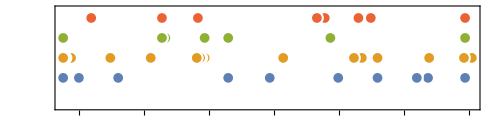

```mathematica
TimelinePlot[
	Table[
		DayRange[
			DateObject[{2018, 1, 1}],
			DateObject[{2018, 12, 31}],
			"Holiday",
			HolidayCalendar->c
		],
		{c, countries}
	],
	PlotLegends -> countries
]
```